{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{0,10.0124},{5,10.2552},{7,10.3378},{9,10.4132},{12,10.5141},{14,10.574},{16,10.6286},{19,10.7016},{21,10.7449},{23,10.7845},{26,10.8373},{28,10.8687},{30,10.8974},{33,10.9357}}

{{0,10.0124},{5,10.2017},{7,10.5397},{9,10.4451},{12,10.4856},{14,10.702},{16,10.702},{19,10.8642},{21,10.8237},{23,10.9859},{26,11.1346},{28,11.1617},{30,11.3239},{33,11.2563}}

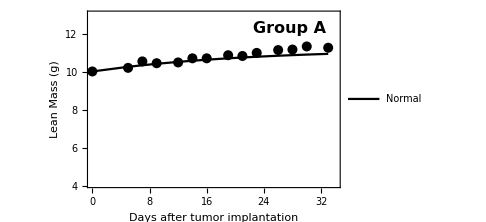

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;m=1000;d=0.05;
s=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==250.31,M[0]==4755.9},{S,M},{x,0,500}]
jm1=(0.002*M[0]/.s)[[1]];jm2=(0.002*M[5]/.s)[[1]];jm3=(0.002*M[7]/.s)[[1]];jm4=(0.002*M[9]/.s)[[1]];jm5=(0.002*M[12]/.s)[[1]];jm6=(0.002*M[14]/.s)[[1]];jm7=(0.002*M[16]/.s)[[1]];jm8=(0.002*M[19]/.s)[[1]];jm9=(0.002*M[21]/.s)[[1]];jm10=(0.002*M[23]/.s)[[1]];jm11=(0.002*M[26]/.s)[[1]];jm12=(0.002*M[28]/.s)[[1]];
jm13=(0.002*M[30]/.s)[[1]];
jm14=(0.002*M[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%*)
js1=(0.002*S[0]/.s)[[1]];js2=(0.002*S[5]/.s)[[1]];js3=(0.002*S[7]/.s)[[1]];js4=(0.002*S[9]/.s)[[1]];js5=(0.002*S[12]/.s)[[1]];js6=(0.002*S[14]/.s)[[1]];js7=(0.002*S[16]/.s)[[1]];js8=(0.002*S[19]/.s)[[1]];js9=(0.002*S[21]/.s)[[1]];js10=(0.002*S[23]/.s)[[1]];js11=(0.002*S[26]/.s)[[1]];js12=(0.002*S[28]/.s)[[1]];
js13=(0.002*S[30]/.s)[[1]];
js14=(0.002*S[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
j1=jm1+js1;
j2=jm2+js2;
j3=jm3+js3;
j4=jm4+js4;
j5=jm5+js5;
j6=jm6+js6;
j7=jm7+js7;
j8=jm8+js8;
j9=jm9+js9;
j10=jm10+js10;
j11=jm11+js11;
j12=jm12+js12;
j13=jm13+js13;
j14=jm14+js14;
data1=List[{0,j1},{5,j2},{7,j3},{9,j4},{12,j5},{14,j6},{16,j7},{19,j8},{21,j9},{23,j10},{26,j11},{28,j12},{30,j13},{33,j14}]
data2=Import["D:/LBMblack1.txt",{"Data",{All},{1,2}}]
G1=ListLinePlot[Split[data1,#2=!={0,0}&],(*PlotMarkers->{Automatic,Medium},*)PlotStyle->{Black,Thickness[0.01]},AxesStyle->Directive[Black,12],PlotLegends->Placed[LineLegend[{"Normal"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.2,0.3}],PlotRange->{{-0.0001,34},{4.1,13}}];
pl1=Show[G1,ListPlot[data2,PlotStyle->{Black,PointSize[0.02]},ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Lean Mass (g)",18(*,Bold*)]},LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,12],  FrameTicksStyle->Directive[Black,14],Epilog->Text[Style["Group A",Black,Bold,Italic,16,FontFamily->"Times New Roman"],Scaled[{.8,.9}]]]
```

{{0,10.0992},{5,9.83952},{7,9.59825},{9,9.3092},{12,8.81812},{14,8.46898},{16,8.11267},{19,7.57899},{21,7.23102},{23,6.89371},{26,6.41379},{28,6.11426},{30,5.83287},{33,5.44728}}

{{0,10.0991},{5,10.3081},{7,10.353},{9,10.3363},{12,9.95988},{14,9.73706},{16,9.2575},{19,7.67494},{21,7.34486},{23,6.8773},{26,6.16878},{28,5.73076},{30,5.62033},{33,4.76201}}

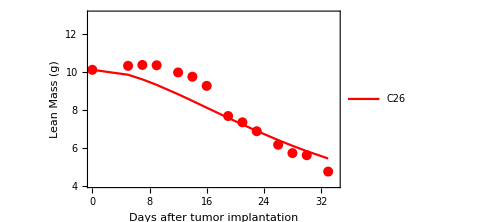

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.49941;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;d2=0.0;
s=NDSolve[{T'[x]==(0.244597*T[x])/((1+(T[x]/1088.66)^μ)^(1/μ)),S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-ϵ*T[x]/(1+T[x]/m2))*S[x]-((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-ϵ*T[x]/(1+T[x]/m2))* S[x]-(d+((d2*T[x])/(1+(T[x]/m2))))*M[x],T[0]==6.86,S[0]==252.5,M[0]==4797.08},{T,S,M},{x,0,100}];

jm1=(0.002*M[0]/.s)[[1]];jm2=(0.002*M[5]/.s)[[1]];jm3=(0.002*M[7]/.s)[[1]];jm4=(0.002*M[9]/.s)[[1]];jm5=(0.002*M[12]/.s)[[1]];jm6=(0.002*M[14]/.s)[[1]];jm7=(0.002*M[16]/.s)[[1]];jm8=(0.002*M[19]/.s)[[1]];jm9=(0.002*M[21]/.s)[[1]];jm10=(0.002*M[23]/.s)[[1]];jm11=(0.002*M[26]/.s)[[1]];jm12=(0.002*M[28]/.s)[[1]];
jm13=(0.002*M[30]/.s)[[1]];
jm14=(0.002*M[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%*)
js1=(0.002*S[0]/.s)[[1]];js2=(0.002*S[5]/.s)[[1]];js3=(0.002*S[7]/.s)[[1]];js4=(0.002*S[9]/.s)[[1]];js5=(0.002*S[12]/.s)[[1]];js6=(0.002*S[14]/.s)[[1]];js7=(0.002*S[16]/.s)[[1]];js8=(0.002*S[19]/.s)[[1]];js9=(0.002*S[21]/.s)[[1]];js10=(0.002*S[23]/.s)[[1]];js11=(0.002*S[26]/.s)[[1]];js12=(0.002*S[28]/.s)[[1]];
js13=(0.002*S[30]/.s)[[1]];
js14=(0.002*S[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
jt1=(0.002*T[0]/.s)[[1]];jt2=(0.002*T[5]/.s)[[1]];jt3=(0.002*T[7]/.s)[[1]];jt4=(0.002*T[9]/.s)[[1]];jt5=(0.002*T[12]/.s)[[1]];jt6=(0.002*T[14]/.s)[[1]];jt7=(0.002*T[16]/.s)[[1]];jt8=(0.002*T[19]/.s)[[1]];jt9=(0.002*T[21]/.s)[[1]];jt10=(0.002*T[23]/.s)[[1]];jt11=(0.002*T[26]/.s)[[1]];jt12=(0.002*T[28]/.s)[[1]];
jt13=(0.002*T[30]/.s)[[1]];
jt14=(0.002*T[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
j1=jm1+js1;
j2=jm2+js2;
j3=jm3+js3;
j4=jm4+js4;
j5=jm5+js5;
j6=jm6+js6;
j7=jm7+js7;
j8=jm8+js8;
j9=jm9+js9;
j10=jm10+js10;
j11=jm11+js11;
j12=jm12+js12;
j13=jm13+js13;
j14=jm14+js14;
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
data1=List[{0,j1},{5,j2},{7,j3},{9,j4},{12,j5},{14,j6},{16,j7},{19,j8},{21,j9},{23,j10},{26,j11},{28,j12}, {30,j13}, {33,j14} ]
data2=Import["D:/LBM.txt",{"Data",{All},{1,2}}]
G1=ListLinePlot[Split[data1,#2=!={0,0}&](*,PlotMarkers->{Automatic,Medium}*),PlotStyle->{Red,Thickness[0.01]},AxesStyle->Directive[Black,12],PlotLegends->Placed[LineLegend[{"C26"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.16,0.2}],PlotRange->{{-0.0001,34},{4.1,13}}];
pl2=Show[G1,ListPlot[data2,PlotStyle->{Red,PointSize[0.02]},ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Lean Mass (g)",18(*,Bold*)]},LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,12],  FrameTicksStyle->Directive[Black,14]]
```

{{5,9.75258},{7,10.0657},{9,10.276},{12,10.4384},{14,10.4653},{16,10.4405},{19,10.3261},{21,10.2089},{23,10.0659},{26,9.81378},{28,9.62639},{30,9.42741},{33,9.11314}}

{{0,9.99223},{5,10.2139},{7,10.8089},{9,11.3686},{12,11.7067},{14,11.6785},{16,11.4649},{19,10.9707},{21,10.4066},{23,9.90646},{26,9.39526},{28,9.17663},{30,9.1489},{33,8.55804}}

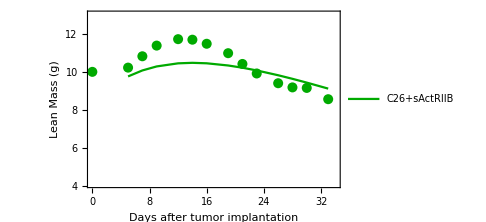

9.38261

0.369928

0.0453568

{{0,9.99248},{5,9.75254}}

{{0,9.99223},{5,10.2139},{7,10.8089},{9,11.3686},{12,11.7067},{14,11.6785},{16,11.4649},{19,10.9707},{21,10.4066},{23,9.90646},{26,9.39526},{28,9.17663},{30,9.1489},{33,8.55804}}

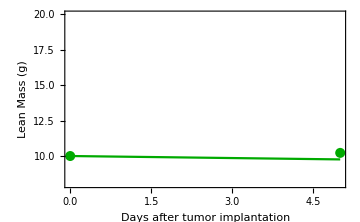

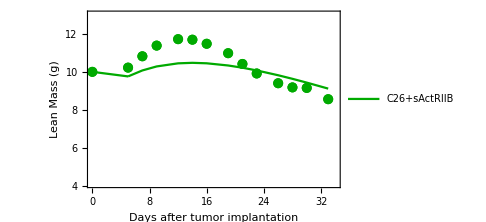

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;A1=0.0;A2=0.89;A3=0.4;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))*S[x]-A2*((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))* S[x]-A3*d*M[x],T[5]==22.68,S[5]==184.98,M[5]==4691.31},{T,S,M},{x,5,100}];
(*jm1=(0.002*M[0]/.s)[[1]];*)
jm2=(0.002*M[5]/.s)[[1]];jm3=(0.002*M[7]/.s)[[1]];jm4=(0.002*M[9]/.s)[[1]];jm5=(0.002*M[12]/.s)[[1]];jm6=(0.002*M[14]/.s)[[1]];jm7=(0.002*M[16]/.s)[[1]];jm8=(0.002*M[19]/.s)[[1]];jm9=(0.002*M[21]/.s)[[1]];jm10=(0.002*M[23]/.s)[[1]];jm11=(0.002*M[26]/.s)[[1]];jm12=(0.002*M[28]/.s)[[1]];
jm13=(0.002*M[30]/.s)[[1]];
jm14=(0.002*M[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%*)
(*js1=(0.002*S[0]/.s)[[1]];*)
js2=(0.002*S[5]/.s)[[1]];js3=(0.002*S[7]/.s)[[1]];js4=(0.002*S[9]/.s)[[1]];js5=(0.002*S[12]/.s)[[1]];js6=(0.002*S[14]/.s)[[1]];js7=(0.002*S[16]/.s)[[1]];js8=(0.002*S[19]/.s)[[1]];js9=(0.002*S[21]/.s)[[1]];js10=(0.002*S[23]/.s)[[1]];js11=(0.002*S[26]/.s)[[1]];js12=(0.002*S[28]/.s)[[1]];
js13=(0.002*S[30]/.s)[[1]];
js14=(0.002*S[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*jt1=(0.002*T[0]/.s)[[1]];*)
jt2=(0.002*T[5]/.s)[[1]];jt3=(0.002*T[7]/.s)[[1]];jt4=(0.002*T[9]/.s)[[1]];jt5=(0.002*T[12]/.s)[[1]];jt6=(0.002*T[14]/.s)[[1]];jt7=(0.002*T[16]/.s)[[1]];jt8=(0.002*T[19]/.s)[[1]];jt9=(0.002*T[21]/.s)[[1]];jt10=(0.002*T[23]/.s)[[1]];jt11=(0.002*T[26]/.s)[[1]];jt12=(0.002*T[28]/.s)[[1]];
jt13=(0.002*T[30]/.s)[[1]];
jt14=(0.002*T[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*j1=jm1+js1+jt1+14.988761408571424;*)
j2=jm2+js2;
j3=jm3+js3;
j4=jm4+js4;
j5=jm5+js5;
j6=jm6+js6;
j7=jm7+js7;
j8=jm8+js8;
j9=jm9+js9;
j10=jm10+js10;
j11=jm11+js11;
j12=jm12+js12;
j13=jm13+js13;
j14=jm14+js14;
data1=List[(*{0,j1},*){5,j2},{7,j3},{9,j4},{12,j5},{14,j6},{16,j7},{19,j8},{21,j9},{23,j10},{26,j11},{28,j12}, {30,j13}, {33,j14} ]
data2=Import["D:/green.txt",{"Data",{All},{1,2}}]
(*error=Import["D:/greenerror.txt",{"Data",{All},{1}}]
withError=Transpose[{data2[[All,1]],data2[[All,2]],error}]
Needs["ErrorBarPlots`"]*)
G1=ListLinePlot[Split[data1,#2=!={0,0}&](*,PlotMarkers->{Automatic,Medium}*),PlotStyle->{Darker[Green],Thickness[0.01]},AxesStyle->Directive[Black,12],PlotLegends->Placed[LineLegend[{"C26+sActRIIB"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.265,0.1}],PlotRange->{{-0.0001,34},{4.1,13}}];
pl11=Show[G1,ListPlot[data2,PlotStyle->{Darker[Green],PointSize[0.02]},ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Lean Mass (g)",18(*,Bold*)]},LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,12],  FrameTicksStyle->Directive[Black,14]]



P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;
s2=NDSolve[{TT'[x]-(0.239141*TT[x])/((1+(TT[x]/1008.25)^μ)^(1/μ))==0,SS'[x]==(2 *(P0+P1/(1+MM[x]/m))-1)* (v0+v1/(1+MM[x]/m)-(ϵ*TT[x]/(1+TT[x]/m2)))*SS[x]-((d1*TT[x])/(1+(TT[x]/m2)))*SS[x],MM'[x]==2 *(1-P0-P1/(1+MM[x]/m))*(v0+v1/(1+MM[x]/m)-(ϵ*TT[x]/(1+TT[x]/m2)))* SS[x]-d*MM[x],TT[0]==6.86,SS[0]==249.8,MM[0]==4746.44},{TT,SS,MM},{x,0,100}];
jmm1=(0.002*MM[0]/.s2)[[1]];
jmm2=(0.002*MM[5]/.s2)[[1]]
(*%%%%%%%%%%%%%%%%%%%%%%*)
jss1=(0.002*SS[0]/.s2)[[1]];
jss2=(0.002*SS[5]/.s2)[[1]]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
jtt1=(0.002*TT[0]/.s2)[[1]];
 jtt2=(0.002*TT[5]/.s2)[[1]]
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
jj1=jmm1+jss1;
jj2=jmm2+jss2;
data3=List[{0,jj1},{5,jj2}]
data4=Import["D:/green.txt",{"Data",{All},{1,2}}]
(*error=Import["D:/greenerror.txt",{"Data",{All},{1}}]
withError=Transpose[{data4[[All,1]],data4[[All,2]],error}]
Needs["ErrorBarPlots`"]*)
G2=ListLinePlot[Split[data3,#2=!={0,0}&](*,PlotMarkers->{Automatic,Medium}*),PlotStyle->{Darker[Green],Thickness[0.01]},AxesStyle->Directive[Black,12],PlotRange->{{0,5},{8,20}}];
pl12=Show[G2,ListPlot[data4,PlotStyle->{Darker[Green],PointSize[0.02]},ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Lean Mass (g)",18(*,Bold*)]},LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,12],  FrameTicksStyle->Directive[Black,14]]
pl3=Show[pl11,pl12]
```

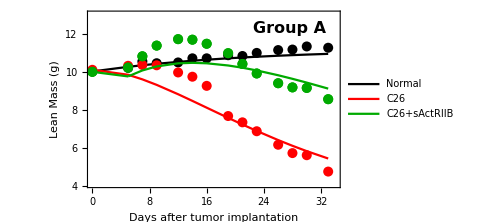

```mathematica
ppl1=Show[pl1,pl2,pl3]
```

{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{0,9.8506},{3,10.0192},{5,10.1199},{7,10.2121},{10,10.3359},{12,10.4097},{14,10.4771},{17,10.5675},{19,10.6214},{21,10.6705},{24,10.7365},{26,10.7757},{28,10.8116},{31,10.8598},{33,10.8885},{35,10.9147},{38,10.9499},{40,10.971}}

{{0,9.85055},{3,9.70549},{5,9.95604},{7,9.95604},{10,10.167},{12,10.2725},{14,10.3912},{17,10.4835},{19,10.4703},{21,10.6022},{24,10.6418},{26,10.5626},{28,10.6022},{31,10.8396},{33,10.8527},{35,10.8923},{38,10.9846},{40,10.9846}}

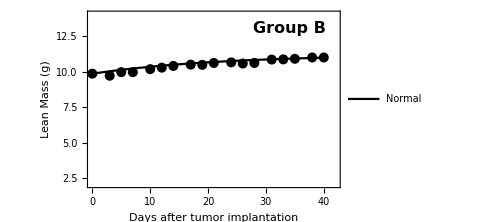

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

P0=0.479;P1=0.133;v0=0.087;v1=5.591;m=1000;d=0.05;
s=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==246.3,M[0]==4679.0},{S,M},{x,0,500}]
jm1=(0.002*M[0]/.s)[[1]];
jm2=(0.002*M[3]/.s)[[1]];jm3=(0.002*M[5]/.s)[[1]];jm4=(0.002*M[7]/.s)[[1]];jm5=(0.002*M[10]/.s)[[1]];jm6=(0.002*M[12]/.s)[[1]];jm7=(0.002*M[14]/.s)[[1]];jm8=(0.002*M[17]/.s)[[1]];jm9=(0.002*M[19]/.s)[[1]];jm10=(0.002*M[21]/.s)[[1]];jm11=(0.002*M[24]/.s)[[1]];jm12=(0.002*M[26]/.s)[[1]];jm13=(0.002*M[28]/.s)[[1]];
jm14=(0.002*M[31]/.s)[[1]];
jm15=(0.002*M[33]/.s)[[1]];
jm16=(0.002*M[35]/.s)[[1]];
jm17=(0.002*M[38]/.s)[[1]];
jm18=(0.002*M[40]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%*)
js1=(0.002*S[0]/.s)[[1]];
js2=(0.002*S[3]/.s)[[1]];js3=(0.002*S[5]/.s)[[1]];js4=(0.002*S[7]/.s)[[1]];js5=(0.002*S[10]/.s)[[1]];js6=(0.002*S[12]/.s)[[1]];js7=(0.002*S[14]/.s)[[1]];js8=(0.002*S[17]/.s)[[1]];js9=(0.002*S[19]/.s)[[1]];js10=(0.002*S[21]/.s)[[1]];js11=(0.002*S[24]/.s)[[1]];js12=(0.002*S[26]/.s)[[1]];js13=(0.002*S[28]/.s)[[1]];
js14=(0.002*S[31]/.s)[[1]];
js15=(0.002*S[33]/.s)[[1]];
js16=(0.002*S[35]/.s)[[1]];
js17=(0.002*S[38]/.s)[[1]];
js18=(0.002*S[40]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
j1=jm1+js1;
j2=jm2+js2;
j3=jm3+js3;
j4=jm4+js4;
j5=jm5+js5;
j6=jm6+js6;
j7=jm7+js7;
j8=jm8+js8;
j9=jm9+js9;
j10=jm10+js10;
j11=jm11+js11;
j12=jm12+js12;
j13=jm13+js13;
j14= jm14+js14;
j15=jm15+js15;
j16=jm16+js16;
j17=jm17+js17;
j18=jm18+js18;
data1=List[{0,j1},{3,j2},{5,j3},{7,j4},{10,j5},{12,j6},{14,j7},{17,j8},{19,j9},{21,j10},{24,j11},{26,j12},{28,j13},{31,j14}, {33,j15},{35,j16},{38,j17},{40,j18}]
data2=Import["D:/black2.txt",{"Data",{All},{1,2}}]
(*error=Import["D:/errorblack2.txt",{"Data",{All},{1}}]
withError=Transpose[{data2[[All,1]],data2[[All,2]],error}]
Needs["ErrorBarPlots`"]*)
(*G1=ListLinePlot[Split[data1,#2=!={0,0}&],PlotMarkers->Automatic,AxesLabel->{"Time (days)","Body weight (grams)"},AxesStyle->Directive[Black,12],PlotLegends->{"Normal"},PlotRange->{{-0.001,42},{0,15}},PlotStyle->Black];*)
G1=ListLinePlot[Split[data1,#2=!={0,0}&](*,PlotMarkers->{Automatic,Medium}*),PlotStyle->{Black,Thickness[0.01]},AxesStyle->Directive[Black,12],PlotLegends->Placed[LineLegend[{"Normal"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.2,0.3}],PlotRange->{{-0.0001,42},{2.1,14}}];
p1=Show[G1,ListPlot[data2,PlotStyle->{Black,PointSize[0.02]},ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Lean Mass (g)",18(*,Bold*)]},LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,12],  FrameTicksStyle->Directive[Black,14],Epilog->Text[Style["Group B",Black,Bold,Italic,16,FontFamily->"Times New Roman"],Scaled[{.8,.9}]]]
```

{{0,10.0356},{3,9.95767},{5,9.78748},{7,9.55052},{10,9.10994},{12,8.78025},{14,8.43467},{17,7.9046},{19,7.55267},{21,7.20755},{24,6.71043},{26,6.39667},{28,6.0994},{31,5.68761},{33,5.43745},{35,5.20775},{38,4.9029},{40,4.72681}}

{{0,10.0351},{3,9.87043},{5,10.1256},{7,10.1132},{10,10.1977},{12,9.98613},{14,9.27588},{17,7.81713},{19,7.15161},{21,6.94637},{24,6.13276},{26,6.00011},{28,5.64094},{31,5.21238},{33,5.10161},{35,4.67503},{38,3.92993},{40,3.2929}}

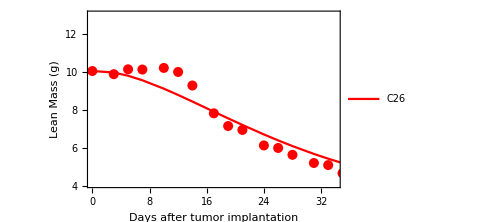

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.49941;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;d2=0.0;
s=NDSolve[{T'[x]==(0.244597*T[x])/((1+(T[x]/1088.66)^μ)^(1/μ)),S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-ϵ*T[x]/(1+T[x]/m2))*S[x]-((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-ϵ*T[x]/(1+T[x]/m2))* S[x]-(d+((d2*T[x])/(1+(T[x]/m2))))*M[x],T[0]==6.86,S[0]==250.89,M[0]==4766.9},{T,S,M},{x,0,100}];
jm1=(0.002*M[0]/.s)[[1]];
jm2=(0.002*M[3]/.s)[[1]];jm3=(0.002*M[5]/.s)[[1]];jm4=(0.002*M[7]/.s)[[1]];jm5=(0.002*M[10]/.s)[[1]];jm6=(0.002*M[12]/.s)[[1]];jm7=(0.002*M[14]/.s)[[1]];jm8=(0.002*M[17]/.s)[[1]];jm9=(0.002*M[19]/.s)[[1]];jm10=(0.002*M[21]/.s)[[1]];jm11=(0.002*M[24]/.s)[[1]];jm12=(0.002*M[26]/.s)[[1]];jm13=(0.002*M[28]/.s)[[1]];
jm14=(0.002*M[31]/.s)[[1]];
jm15=(0.002*M[33]/.s)[[1]];
jm16=(0.002*M[35]/.s)[[1]];
jm17=(0.002*M[38]/.s)[[1]];
jm18=(0.002*M[40]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%*)
js1=(0.002*S[0]/.s)[[1]];
js2=(0.002*S[3]/.s)[[1]];js3=(0.002*S[5]/.s)[[1]];js4=(0.002*S[7]/.s)[[1]];js5=(0.002*S[10]/.s)[[1]];js6=(0.002*S[12]/.s)[[1]];js7=(0.002*S[14]/.s)[[1]];js8=(0.002*S[17]/.s)[[1]];js9=(0.002*S[19]/.s)[[1]];js10=(0.002*S[21]/.s)[[1]];js11=(0.002*S[24]/.s)[[1]];js12=(0.002*S[26]/.s)[[1]];js13=(0.002*S[28]/.s)[[1]];
js14=(0.002*S[31]/.s)[[1]];
js15=(0.002*S[33]/.s)[[1]];
js16=(0.002*S[35]/.s)[[1]];
js17=(0.002*S[38]/.s)[[1]];
js18=(0.002*S[40]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
jt1=(0.002*T[0]/.s)[[1]];
jt2=(0.002*T[3]/.s)[[1]];jt3=(0.002*T[5]/.s)[[1]];jt4=(0.002*T[7]/.s)[[1]];jt5=(0.002*T[10]/.s)[[1]];jt6=(0.002*T[12]/.s)[[1]];jt7=(0.002*T[14]/.s)[[1]];jt8=(0.002*T[17]/.s)[[1]];jt9=(0.002*T[19]/.s)[[1]];jt10=(0.002*T[21]/.s)[[1]];jt11=(0.002*T[24]/.s)[[1]];jt12=(0.002*T[26]/.s)[[1]];jt13=(0.002*T[28]/.s)[[1]];
jt14=(0.002*T[31]/.s)[[1]];
jt15=(0.002*T[33]/.s)[[1]];
jt16=(0.002*T[35]/.s)[[1]];
jt17=(0.002*T[38]/.s)[[1]];
jt18=(0.002*T[40]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
j1=jm1+js1;
j2=jm2+js2;
j3=jm3+js3;
j4=jm4+js4;
j5=jm5+js5;
j6=jm6+js6;
j7=jm7+js7;
j8=jm8+js8;
j9=jm9+js9;
j10=jm10+js10;
j11=jm11+js11;
j12=jm12+js12;
j13=jm13+js13;
j14= jm14+js14;
j15=jm15+js15;
j16=jm16+js16;
j17=jm17+js17;
j18=jm18+js18;
data1=List[{0,j1},{3,j2},{5,j3},{7,j4},{10,j5},{12,j6},{14,j7},{17,j8},{19,j9},{21,j10},{24,j11},{26,j12},{28,j13},{31,j14}, {33,j15},{35,j16},{38,j17},{40,j18}]
data2=Import["D:/LBM2.txt",{"Data",{All},{1,2}}]
(*error=Import["D:/Errorbar2.txt",{"Data",{All},{1}}]
withError=Transpose[{data2[[All,1]],data2[[All,2]],error}]
Needs["ErrorBarPlots`"]*)
(*Show[ListLinePlot[data1,PlotStyle->{Line,Thick},PlotRange->{{-0.2,22},{15,30}},AxesLabel->{"Time (days)","Body weight (grams)"},AxesStyle->Directive[Black,12],PlotLegends->{"Model prediction"}],ErrorListPlot[withError,PlotStyle->Red,PlotLegends->{"Experimental data"}]]*)
G1=ListLinePlot[Split[data1,#2=!={0,0}&](*PlotMarkers->{Automatic,Medium}*),PlotStyle->{Red,Thickness[0.01]},AxesStyle->Directive[Black,12],PlotLegends->Placed[LineLegend[{"C26"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.16,0.2}],PlotRange->{{-0.0001,34},{4.1,13}}];
p2=Show[G1,ListPlot[data2,PlotStyle->{Red,PointSize[0.02]},ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Lean Mass (g)",18(*,Bold*)]},LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,12],  FrameTicksStyle->Directive[Black,14]]
```

0.4

{{14,8.41788},{17,8.57978},{19,8.6251},{21,8.6296},{24,8.574},{26,8.50322},{28,8.41074},{31,8.23948},{33,8.10818},{35,7.96627},{38,7.73832},{40,7.57903}}

{{0,10.0033},{3,9.8724},{5,10.125},{7,10.0537},{10,10.0933},{12,9.87052},{14,9.35092},{17,8.49773},{19,8.30116},{21,8.26235},{24,8.13554},{26,7.65016},{28,7.76797},{31,7.57373},{33,7.3471},{35,7.21263},{38,7.10977},{40,6.84339}}

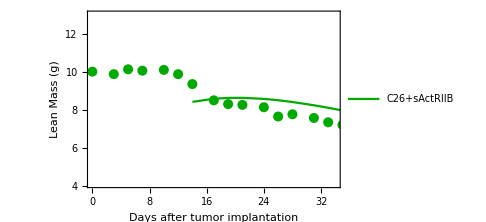

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;A1=0.0;A2=0.89;A3=0.4
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))*S[x]-A2*((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))* S[x]-A3*d*M[x],T[14]==195.13,S[14]==106.939,M[14]==4102},{T,S,M},{x,14,100}];
(*jm1=(0.002*M[0]/.s)[[1]];
jm2=(0.002*M[3]/.s)[[1]];jm3=(0.002*M[5]/.s)[[1]];jm4=(0.002*M[7]/.s)[[1]];jm5=(0.002*M[10]/.s)[[1]];jm6=(0.002*M[12]/.s)[[1]];*)
jm7=(0.002*M[14]/.s)[[1]];jm8=(0.002*M[17]/.s)[[1]];jm9=(0.002*M[19]/.s)[[1]];jm10=(0.002*M[21]/.s)[[1]];jm11=(0.002*M[24]/.s)[[1]];jm12=(0.002*M[26]/.s)[[1]];jm13=(0.002*M[28]/.s)[[1]];
jm14=(0.002*M[31]/.s)[[1]];
jm15=(0.002*M[33]/.s)[[1]];
jm16=(0.002*M[35]/.s)[[1]];
jm17=(0.002*M[38]/.s)[[1]];
jm18=(0.002*M[40]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%*)
(*js1=(0.002*S[0]/.s)[[1]];
js2=(0.002*S[3]/.s)[[1]];js3=(0.002*S[5]/.s)[[1]];js4=(0.002*S[7]/.s)[[1]];js5=(0.002*S[10]/.s)[[1]];js6=(0.002*S[12]/.s)[[1]];*)
js7=(0.002*S[14]/.s)[[1]];js8=(0.002*S[17]/.s)[[1]];js9=(0.002*S[19]/.s)[[1]];js10=(0.002*S[21]/.s)[[1]];js11=(0.002*S[24]/.s)[[1]];js12=(0.002*S[26]/.s)[[1]];js13=(0.002*S[28]/.s)[[1]];
js14=(0.002*S[31]/.s)[[1]];
js15=(0.002*S[33]/.s)[[1]];
js16=(0.002*S[35]/.s)[[1]];
js17=(0.002*S[38]/.s)[[1]];
js18=(0.002*S[40]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*jt1=(0.002*T[0]/.s)[[1]];
jt2=(0.002*T[3]/.s)[[1]];jt3=(0.002*T[5]/.s)[[1]];jt4=(0.002*T[7]/.s)[[1]];jt5=(0.002*T[10]/.s)[[1]];jt6=(0.002*T[12]/.s)[[1]];*)
jt7=(0.002*T[14]/.s)[[1]];jt8=(0.002*T[17]/.s)[[1]];jt9=(0.002*T[19]/.s)[[1]];jt10=(0.002*T[21]/.s)[[1]];jt11=(0.002*T[24]/.s)[[1]];jt12=(0.002*T[26]/.s)[[1]];jt13=(0.002*T[28]/.s)[[1]];
jt14=(0.002*T[31]/.s)[[1]];
jt15=(0.002*T[33]/.s)[[1]];
jt16=(0.002*T[35]/.s)[[1]];
jt17=(0.002*T[38]/.s)[[1]];
jt18=(0.002*T[40]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(*j1=jm1+jss1+jtt1+15.005353690141742;j2=jm2+jss2+jtt2+14.82056023366874;j3=jmm3+jss3+jtt3+15.207334331475879;j4=jmm4+jss4+jtt4+15.113326656457652;j5=jmm5+jss5+jtt5+15.209507701028155;j6=jmm6+jss6+jtt6+14.920825278008387;*)
j7=jm7+js7;
j8=jm8+js8;
j9=jm9+js9;
j10=jm10+js10;
j11=jm11+js11;
j12=jm12+js12;
j13=jm13+js13;
j14= jm14+js14;
j15=jm15+js15;
j16=jm16+js16;
j17=jm17+js17;
j18=jm18+js18;
data1=List[(*{0,j1},{3,j2},{5,j3},{7,j4},{10,j5},{12,j6},*){14,j7},{17,j8},{19,j9},{21,j10},{24,j11},{26,j12},{28,j13},{31,j14}, {33,j15},{35,j16},{38,j17},{40,j18}]
data2=Import["D:/green2.txt",{"Data",{All},{1,2}}]
(*error=Import["D:/greenerror2.txt",{"Data",{All},{1}}]
withError=Transpose[{data2[[All,1]],data2[[All,2]],error}]
Needs["ErrorBarPlots`"]*)
G1=ListLinePlot[Split[data1,#2=!={0,0}&](*,PlotMarkers->{Automatic,Medium}*),PlotStyle->{Darker[Green],Thickness[0.01]},AxesStyle->Directive[Black,12],PlotLegends->Placed[LineLegend[{"C26+sActRIIB"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.265,0.1}],PlotRange->{{-0.0001,34},{4.1,13}}];
pl1=Show[G1,ListPlot[data2,PlotStyle->{Darker[Green],PointSize[0.02]},ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Lean Mass (g)",18(*,Bold*)]},LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,12],  FrameTicksStyle->Directive[Black,14]]
```

{{0,10.0017},{3,9.92284},{5,9.75148},{7,9.51367},{10,9.07274},{12,8.74344},{14,8.39868}}

{{0,10.0033},{3,9.8724},{5,10.125},{7,10.0537},{10,10.0933},{12,9.87052},{14,9.35092},{17,8.49773},{19,8.30116},{21,8.26235},{24,8.13554},{26,7.65016},{28,7.76797},{31,7.57373},{33,7.3471},{35,7.21263},{38,7.10977},{40,6.84339}}

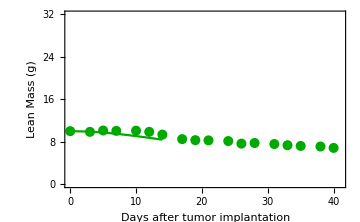

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;
s2=NDSolve[{TT'[x]-(0.239141*TT[x])/((1+(TT[x]/1008.25)^μ)^(1/μ))==0,SS'[x]==(2 *(P0+P1/(1+MM[x]/m))-1)* (v0+v1/(1+MM[x]/m)-(ϵ*TT[x]/(1+TT[x]/m2)))*SS[x]-((d1*TT[x])/(1+(TT[x]/m2)))*SS[x],MM'[x]==2 *(1-P0-P1/(1+MM[x]/m))*(v0+v1/(1+MM[x]/m)-(ϵ*TT[x]/(1+TT[x]/m2)))* SS[x]-d*MM[x],TT[0]==8.88,SS[0]==250.042,MM[0]==4750.8},{TT,SS,MM},{x,0,100}];
jmm1=(0.002*MM[0]/.s2)[[1]];
jmm2=(0.002*MM[3]/.s2)[[1]];
jmm3=(0.002*MM[5]/.s2)[[1]];
jmm4=(0.002*MM[7]/.s2)[[1]];
jmm5=(0.002*MM[10]/.s2)[[1]];
jmm6=(0.002*MM[12]/.s2)[[1]];
jmm7=(0.002*MM[14]/.s2)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%*)
jss1=(0.002*SS[0]/.s2)[[1]];
jss2=(0.002*SS[3]/.s2)[[1]];
jss3=(0.002*SS[5]/.s2)[[1]];
jss4=(0.002*SS[7]/.s2)[[1]];
jss5=(0.002*SS[10]/.s2)[[1]];
jss6=(0.002*SS[12]/.s2)[[1]];
jss7=(0.002*SS[14]/.s2)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
jtt1=(0.002*TT[0]/.s2)[[1]];
jtt2=(0.002*TT[3]/.s2)[[1]];
jtt3=(0.002*TT[5]/.s2)[[1]];
jtt4=(0.002*TT[7]/.s2)[[1]];
jtt5=(0.002*TT[10]/.s2)[[1]];
jtt6=(0.002*TT[12]/.s2)[[1]];
jtt7=(0.002*TT[14]/.s2)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
jj1=jmm1+jss1;
jj2=jmm2+jss2;
jj3=jmm3+jss3;
jj4=jmm4+jss4;
jj5=jmm5+jss5;
jj6=jmm6+jss6;
jj7=jmm7+jss7;
data3=List[{0,jj1},{3,jj2},{5,jj3},{7,jj4},{10,jj5},{12,jj6},{14,jj7}]
data4=Import["D:/green2.txt",{"Data",{All},{1,2}}]
(*error=Import["D:/greenerror2.txt",{"Data",{All},{1}}]
withError=Transpose[{data4[[All,1]],data4[[All,2]],error}]
Needs["ErrorBarPlots`"]*)
G2=ListLinePlot[Split[data3,#2=!={0,0}&](*,PlotMarkers->{Automatic,Medium}*),PlotStyle->{Darker[Green],Thickness[0.01]},AxesStyle->Directive[Black,12],PlotRange->{{0,41},{0,32}}];
pl2=Show[G2,ListPlot[data4,PlotStyle->{Darker[Green],PointSize[0.02]},ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{Style["Days after tumor implantation",18(*,Bold*)],Style["Lean Mass (g)",18(*,Bold*)]},LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameStyle->Directive[Black,12],  FrameTicksStyle->Directive[Black,14]]
```

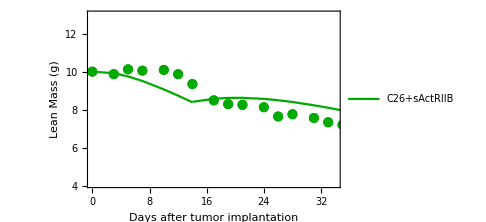

```mathematica
p3=Show[pl1,pl2]
```

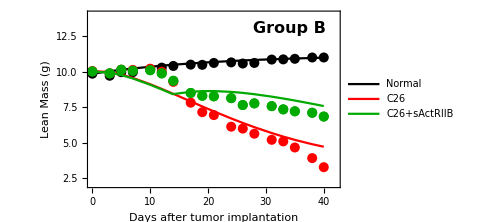

```mathematica
ppl2=Show[p1,p2,p3]
```

```mathematica
d1=Show[ppl1]
```

-Graphics-

```mathematica
d2=Show[ppl2]
```

-Graphics-

```mathematica
Export["D:/All1.eps",d1]
```

D:/All1.eps

```mathematica
Export["D:/All2.eps",d2]
```

D:/All2.eps